# Teste 1 ISD

# Diogo Nogueira A78957 Diogo Araújo A78485

## Question 1

```mathematica
DSolve[ {x'[t] == (x[t]*(x[t]-2)),x[0]==1},x[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x[t]→2/(1+ⅇ^(2 t))}}

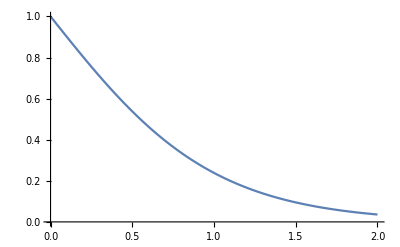

```mathematica
Plot[2/(1+ⅇ^(2 t)), {t,0,2}]
```

## Question 2

```mathematica
DSolve[ x'[t] == (-(x[t])/ (t^2)),x[t],t]
```

{{x[t]→ⅇ^(1/t) C[1]}}

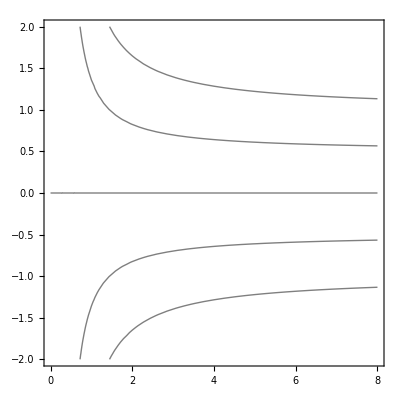

```mathematica
ContourPlot[x*Exp[-(1/t)],{t,0,8},{x,-2,2}, ContourShading->False,Contours->{-1,-0.5,0,0.5,1},Axes->True]
```